```mathematica
(* V.V. Albert 2016 Eq. 5.8 which is incorrect *)
1/(4 √(2(Cosh[α^2]+(-1)^μ Cos[α^2])));
```

```mathematica
ℳ[μ_,ϵ_,α_]:=(1-ϵ)/(2 √(2 ⅇ^(-α^2)(Cosh[α^2]+(-1)^μ Cos[α^2])))+ϵ/(2 √(2 ⅇ^(-α^2)(Sinh[α^2]-(-1)^μ Sin[α^2])));
```

```mathematica
ℳ[0,0,α]
ℳ[1,0,α]
ℳ[0,1,α]
ℳ[1,1,α]
```

1/(2 √2 √(ⅇ^(-α^2) (Cos[α^2]+Cosh[α^2])))

1/(2 √2 √(ⅇ^(-α^2) (-Cos[α^2]+Cosh[α^2])))

1/(2 √2 √(ⅇ^(-α^2) (-Sin[α^2]+Sinh[α^2])))

1/(2 √2 √(ⅇ^(-α^2) (Sin[α^2]+Sinh[α^2])))

```mathematica
(* k =4n *)
mat[4n,0]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]+Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];
mat[4n,1]=0;
mat[4n,2]=0;
mat[4n,3]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]-Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];

(* k = 4n+2 *)
mat[4n+2,0]=0;
mat[4n+2,1]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]+Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];
mat[4n+2,2]=ⅈ Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,0,√γ α])^2),{α>0,0<γ<1}]-ⅈ Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,0,√γ α])^2),{α>0,0<γ<1}];
mat[4n+2,3]=0;

(* k =4n+1 *)
mat[4n+1,0]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]+Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];
mat[4n+1,1]=0;
mat[4n+1,2]=0;
mat[4n+1,3]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];

(* k = 4n+3 *)
mat[4n+3,0]=0;
mat[4n+3,1]=Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]+Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];
mat[4n+3,2]=ⅈ Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[1,0,α])/ℳ[0,1,√γ α])^2),{α>0,0<γ<1}]-ⅈ Simplify[√(((ⅇ^(-α^2/2(1-γ))ℳ[0,0,α])/ℳ[1,1,√γ α])^2),{α>0,0<γ<1}];
mat[4n+3,3]=0;

Zeros = ConstantArray[0,4];
f[n_]=( √(1-γ)α)^n/(√2 √(n!));
w[n_]=
{
(f[4n]mat[4n,#]&/@ Range[0,3,1])~Join~Zeros,
(f[4n+2]mat[4n+2,#]&/@ Range[0,3,1])~Join~Zeros,
Zeros~Join~(f[4n+1]mat[4n+1,#]&/@ Range[0,3,1]),
Zeros~Join~(f[4n+3]mat[4n+3,#]&/@ Range[0,3,1])
};

W[n_,α_,γ_]=Simplify[w[n]ᵀ.w[n]*,{α>0,1>γ>0,n>=0,Sinh[α^2]>Sin[α^2],Cosh[α^2]>Cos[α^2],Sinh[α^2 γ]>Sin[α^2 γ],Cosh[α^2 γ]>Cos[α^2 γ],Sinh[α^2]+Sin[α^2]>0,Cosh[α^2]+Cos[α^2]>0,Sinh[α^2 γ]+Sin[α^2 γ]>0,Cosh[α^2 γ]+Cos[α^2 γ]>0}];
```

```mathematica
Simplify[∑_(n=0)^∞ W[n,α,γ]]
```

```mathematica
ClearAll[𝒲];
𝒲[α_,γ_]={{1/(Cos[2 α^2]-Cosh[2 α^2])(Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cosh[α^2] Cosh[α^2 γ]-Cosh[α^2]^2 √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Cos[α^2 γ]+Cos[α^2] √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),0,0,-((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]-Cos[α^2] Cosh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),0,0,0,0},{0,-1/(Cos[2 α^2]-Cosh[2 α^2])(Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (-Cos[α^2] Cos[α^2 γ]-Cosh[α^2] Cosh[α^2 γ]+Cos[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))),-(ⅈ (Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),0,0,0,0,0},{0,(ⅈ (Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]+Cos[α^2] Cosh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),1/(Cos[2 α^2]-Cosh[2 α^2])(Cos[α^2 (-1+γ)]-Cosh[α^2 (-1+γ)]) (Cos[α^2] Cos[α^2 γ]+Cosh[α^2] Cosh[α^2 γ]+Cos[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))),0,0,0,0,0},{-((Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (Cos[α^2 γ] Cosh[α^2]-Cos[α^2] Cosh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),0,0,1/(Cos[2 α^2]-Cosh[2 α^2])(Cos[α^2 (-1+γ)]+Cosh[α^2 (-1+γ)]) (-Cosh[α^2] Cosh[α^2 γ]+Cosh[α^2]^2 √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Cos[α^2 γ]-Cos[α^2] √((Cos[α^2 γ]-Cosh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Cos[α^2 γ]+Cosh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),0,0,0,0},{0,0,0,0,-1/(Cos[2 α^2]-Cosh[2 α^2])(Sin[α^2 (-1+γ)]+Sinh[α^2 (-1+γ)]) (-Cos[α^2] Sin[α^2 γ]-Cosh[α^2] Sinh[α^2 γ]+Cos[α^2]^2 √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))),0,0,-((Sin[α^2 (-1+γ)]+Sinh[α^2 (-1+γ)]) (Cosh[α^2] Sin[α^2 γ]+Cos[α^2] Sinh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2])},{0,0,0,0,0,1/(Cos[2 α^2]-Cosh[2 α^2])(Sin[α^2 (-1+γ)]-Sinh[α^2 (-1+γ)]) (-Cosh[α^2] Sinh[α^2 γ]-Cosh[α^2]^2 √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Sin[α^2 γ]+Cos[α^2] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),-(ⅈ (Sin[α^2 (-1+γ)]-Sinh[α^2 (-1+γ)]) (Cosh[α^2] Sin[α^2 γ]-Cos[α^2] Sinh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),0},{0,0,0,0,0,(ⅈ (Sin[α^2 (-1+γ)]-Sinh[α^2 (-1+γ)]) (Cosh[α^2] Sin[α^2 γ]-Cos[α^2] Sinh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),1/(Cos[2 α^2]-Cosh[2 α^2])(Sin[α^2 (-1+γ)]-Sinh[α^2 (-1+γ)]) (-Cosh[α^2] Sinh[α^2 γ]+Cosh[α^2]^2 √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2]))+Cos[α^2] (Sin[α^2 γ]-Cos[α^2] √((Sin[α^2 γ]-Sinh[α^2 γ])/(Cos[α^2]-Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])))),0},{0,0,0,0,-((Sin[α^2 (-1+γ)]+Sinh[α^2 (-1+γ)]) (Cosh[α^2] Sin[α^2 γ]+Cos[α^2] Sinh[α^2 γ]))/(Cos[2 α^2]-Cosh[2 α^2]),0,0,1/(Cos[2 α^2]-Cosh[2 α^2])(Sin[α^2 (-1+γ)]+Sinh[α^2 (-1+γ)]) (Cos[α^2] Sin[α^2 γ]+Cosh[α^2] Sinh[α^2 γ]+Cos[α^2]^2 √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2]))-Cosh[α^2]^2 √((-Sin[α^2 γ]+Sinh[α^2 γ])/(Cos[α^2]+Cosh[α^2])) √((Sin[α^2 γ]+Sinh[α^2 γ])/(-Cos[α^2]+Cosh[α^2])))}};
```

```mathematica
Chop[𝒲[2,0.90],10^-3]//MatrixForm
```

(1.34161 | 0 | 0 | -0.0168147 | 0 | 0 | 0 | 0
0 | 0.107348 | 0.+0.00391369 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00391369 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
-0.0168147 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.536097 | 0 | 0 | 0.0129029
0 | 0 | 0 | 0 | 0 | 0.014285 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0129029 | 0 | 0 | 0)

```mathematica
Chop[𝒲odd[2,0.90],10^-3]//MatrixForm
```

(0.0143255 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.536574 | 0.+0.00570602 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0.-0.00570602 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.34165 | 0 | 0 | -0.00237045
0 | 0 | 0 | 0 | 0 | 0.107297 | 0.-0.00278611 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0.+0.00278611 ⅈ | 0 | 0
0 | 0 | 0 | 0 | -0.00237045 | 0 | 0 | 0)

```mathematica
Quiet[Needs["MatLink`"]]
Quiet[OpenMATLAB[]]
```

```mathematica
<<ToMatlab`
```

```mathematica
ToMatlab[𝒲[alpha,gamma]]
```

[(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1).*(cos(alpha.^2.* ...
  ((-1)+gamma))+cosh(alpha.^2.*((-1)+gamma))).*((-1).*cosh(alpha.^2) ...
  .*cosh(alpha.^2.*gamma)+(-1).*cosh(alpha.^2).^2.*((cos(alpha.^2)+( ...
  -1).*cosh(alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+(-1).*cosh( ...
  alpha.^2.*gamma))).^(1/2).*((cos(alpha.^2)+cosh(alpha.^2)).^(-1).* ...
  (cos(alpha.^2.*gamma)+cosh(alpha.^2.*gamma))).^(1/2)+cos(alpha.^2) ...
  .*(cos(alpha.^2.*gamma)+cos(alpha.^2).*((cos(alpha.^2)+(-1).*cosh( ...
  alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+(-1).*cosh(alpha.^2.* ...
  gamma))).^(1/2).*((cos(alpha.^2)+cosh(alpha.^2)).^(-1).*(cos( ...
  alpha.^2.*gamma)+cosh(alpha.^2.*gamma))).^(1/2))),0,0,(-1).*(cos( ...
  2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1).*(cos(alpha.^2.*((-1)+ ...
  gamma))+cosh(alpha.^2.*((-1)+gamma))).*(cos(alpha.^2.*gamma).* ...
  cosh(alpha.^2)+(-1).*cos(alpha.^2).*cosh(alpha.^2.*gamma)),0,0,0, ...
  0;0,(-1).*(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1).*(cos( ...
  alpha.^2.*((-1)+gamma))+(-1).*cosh(alpha.^2.*((-1)+gamma))).*((-1) ...
  .*cos(alpha.^2).*cos(alpha.^2.*gamma)+(-1).*cosh(alpha.^2).*cosh( ...
  alpha.^2.*gamma)+cos(alpha.^2).^2.*((cos(alpha.^2)+cosh(alpha.^2)) ...
  .^(-1).*((-1).*cos(alpha.^2.*gamma)+cosh(alpha.^2.*gamma))).^(1/2) ...
  .*(((-1).*cos(alpha.^2)+cosh(alpha.^2)).^(-1).*(cos(alpha.^2.* ...
  gamma)+cosh(alpha.^2.*gamma))).^(1/2)+(-1).*cosh(alpha.^2).^2.*(( ...
  cos(alpha.^2)+cosh(alpha.^2)).^(-1).*((-1).*cos(alpha.^2.*gamma)+ ...
  cosh(alpha.^2.*gamma))).^(1/2).*(((-1).*cos(alpha.^2)+cosh( ...
  alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+cosh(alpha.^2.*gamma))).^( ...
  1/2)),(sqrt(-1)*(-1)).*(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)) ...
  .^(-1).*(cos(alpha.^2.*((-1)+gamma))+(-1).*cosh(alpha.^2.*((-1)+ ...
  gamma))).*(cos(alpha.^2.*gamma).*cosh(alpha.^2)+cos(alpha.^2).* ...
  cosh(alpha.^2.*gamma)),0,0,0,0,0;0,sqrt(-1).*(cos(2.*alpha.^2)+( ...
  -1).*cosh(2.*alpha.^2)).^(-1).*(cos(alpha.^2.*((-1)+gamma))+(-1).* ...
  cosh(alpha.^2.*((-1)+gamma))).*(cos(alpha.^2.*gamma).*cosh( ...
  alpha.^2)+cos(alpha.^2).*cosh(alpha.^2.*gamma)),(cos(2.*alpha.^2)+ ...
  (-1).*cosh(2.*alpha.^2)).^(-1).*(cos(alpha.^2.*((-1)+gamma))+(-1) ...
  .*cosh(alpha.^2.*((-1)+gamma))).*(cos(alpha.^2).*cos(alpha.^2.* ...
  gamma)+cosh(alpha.^2).*cosh(alpha.^2.*gamma)+cos(alpha.^2).^2.*(( ...
  cos(alpha.^2)+cosh(alpha.^2)).^(-1).*((-1).*cos(alpha.^2.*gamma)+ ...
  cosh(alpha.^2.*gamma))).^(1/2).*(((-1).*cos(alpha.^2)+cosh( ...
  alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+cosh(alpha.^2.*gamma))).^( ...
  1/2)+(-1).*cosh(alpha.^2).^2.*((cos(alpha.^2)+cosh(alpha.^2)).^( ...
  -1).*((-1).*cos(alpha.^2.*gamma)+cosh(alpha.^2.*gamma))).^(1/2).*( ...
  ((-1).*cos(alpha.^2)+cosh(alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+ ...
  cosh(alpha.^2.*gamma))).^(1/2)),0,0,0,0,0;(-1).*(cos(2.*alpha.^2)+ ...
  (-1).*cosh(2.*alpha.^2)).^(-1).*(cos(alpha.^2.*((-1)+gamma))+cosh( ...
  alpha.^2.*((-1)+gamma))).*(cos(alpha.^2.*gamma).*cosh(alpha.^2)+( ...
  -1).*cos(alpha.^2).*cosh(alpha.^2.*gamma)),0,0,(cos(2.*alpha.^2)+( ...
  -1).*cosh(2.*alpha.^2)).^(-1).*(cos(alpha.^2.*((-1)+gamma))+cosh( ...
  alpha.^2.*((-1)+gamma))).*((-1).*cosh(alpha.^2).*cosh(alpha.^2.* ...
  gamma)+cosh(alpha.^2).^2.*((cos(alpha.^2)+(-1).*cosh(alpha.^2)).^( ...
  -1).*(cos(alpha.^2.*gamma)+(-1).*cosh(alpha.^2.*gamma))).^(1/2).*( ...
  (cos(alpha.^2)+cosh(alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+cosh( ...
  alpha.^2.*gamma))).^(1/2)+cos(alpha.^2).*(cos(alpha.^2.*gamma)+( ...
  -1).*cos(alpha.^2).*((cos(alpha.^2)+(-1).*cosh(alpha.^2)).^(-1).*( ...
  cos(alpha.^2.*gamma)+(-1).*cosh(alpha.^2.*gamma))).^(1/2).*((cos( ...
  alpha.^2)+cosh(alpha.^2)).^(-1).*(cos(alpha.^2.*gamma)+cosh( ...
  alpha.^2.*gamma))).^(1/2))),0,0,0,0;0,0,0,0,(-1).*(cos(2.* ...
  alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1).*(sin(alpha.^2.*((-1)+ ...
  gamma))+sinh(alpha.^2.*((-1)+gamma))).*((-1).*cos(alpha.^2).*sin( ...
  alpha.^2.*gamma)+(-1).*cosh(alpha.^2).*sinh(alpha.^2.*gamma)+cos( ...
  alpha.^2).^2.*((cos(alpha.^2)+cosh(alpha.^2)).^(-1).*((-1).*sin( ...
  alpha.^2.*gamma)+sinh(alpha.^2.*gamma))).^(1/2).*(((-1).*cos( ...
  alpha.^2)+cosh(alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+sinh( ...
  alpha.^2.*gamma))).^(1/2)+(-1).*cosh(alpha.^2).^2.*((cos(alpha.^2) ...
  +cosh(alpha.^2)).^(-1).*((-1).*sin(alpha.^2.*gamma)+sinh( ...
  alpha.^2.*gamma))).^(1/2).*(((-1).*cos(alpha.^2)+cosh(alpha.^2)) ...
  .^(-1).*(sin(alpha.^2.*gamma)+sinh(alpha.^2.*gamma))).^(1/2)),0,0, ...
  (-1).*(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1).*(sin( ...
  alpha.^2.*((-1)+gamma))+sinh(alpha.^2.*((-1)+gamma))).*(cosh( ...
  alpha.^2).*sin(alpha.^2.*gamma)+cos(alpha.^2).*sinh(alpha.^2.* ...
  gamma));0,0,0,0,0,(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1) ...
  .*(sin(alpha.^2.*((-1)+gamma))+(-1).*sinh(alpha.^2.*((-1)+gamma))) ...
  .*((-1).*cosh(alpha.^2).*sinh(alpha.^2.*gamma)+(-1).*cosh( ...
  alpha.^2).^2.*((cos(alpha.^2)+(-1).*cosh(alpha.^2)).^(-1).*(sin( ...
  alpha.^2.*gamma)+(-1).*sinh(alpha.^2.*gamma))).^(1/2).*((cos( ...
  alpha.^2)+cosh(alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+sinh( ...
  alpha.^2.*gamma))).^(1/2)+cos(alpha.^2).*(sin(alpha.^2.*gamma)+ ...
  cos(alpha.^2).*((cos(alpha.^2)+(-1).*cosh(alpha.^2)).^(-1).*(sin( ...
  alpha.^2.*gamma)+(-1).*sinh(alpha.^2.*gamma))).^(1/2).*((cos( ...
  alpha.^2)+cosh(alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+sinh( ...
  alpha.^2.*gamma))).^(1/2))),(sqrt(-1)*(-1)).*(cos(2.*alpha.^2)+( ...
  -1).*cosh(2.*alpha.^2)).^(-1).*(sin(alpha.^2.*((-1)+gamma))+(-1).* ...
  sinh(alpha.^2.*((-1)+gamma))).*(cosh(alpha.^2).*sin(alpha.^2.* ...
  gamma)+(-1).*cos(alpha.^2).*sinh(alpha.^2.*gamma)),0;0,0,0,0,0, ...
  sqrt(-1).*(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1).*(sin( ...
  alpha.^2.*((-1)+gamma))+(-1).*sinh(alpha.^2.*((-1)+gamma))).*( ...
  cosh(alpha.^2).*sin(alpha.^2.*gamma)+(-1).*cos(alpha.^2).*sinh( ...
  alpha.^2.*gamma)),(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)).^(-1) ...
  .*(sin(alpha.^2.*((-1)+gamma))+(-1).*sinh(alpha.^2.*((-1)+gamma))) ...
  .*((-1).*cosh(alpha.^2).*sinh(alpha.^2.*gamma)+cosh(alpha.^2).^2.* ...
  ((cos(alpha.^2)+(-1).*cosh(alpha.^2)).^(-1).*(sin(alpha.^2.*gamma) ...
  +(-1).*sinh(alpha.^2.*gamma))).^(1/2).*((cos(alpha.^2)+cosh( ...
  alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+sinh(alpha.^2.*gamma))).^( ...
  1/2)+cos(alpha.^2).*(sin(alpha.^2.*gamma)+(-1).*cos(alpha.^2).*(( ...
  cos(alpha.^2)+(-1).*cosh(alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+( ...
  -1).*sinh(alpha.^2.*gamma))).^(1/2).*((cos(alpha.^2)+cosh( ...
  alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+sinh(alpha.^2.*gamma))).^( ...
  1/2))),0;0,0,0,0,(-1).*(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)) ...
  .^(-1).*(sin(alpha.^2.*((-1)+gamma))+sinh(alpha.^2.*((-1)+gamma))) ...
  .*(cosh(alpha.^2).*sin(alpha.^2.*gamma)+cos(alpha.^2).*sinh( ...
  alpha.^2.*gamma)),0,0,(cos(2.*alpha.^2)+(-1).*cosh(2.*alpha.^2)) ...
  .^(-1).*(sin(alpha.^2.*((-1)+gamma))+sinh(alpha.^2.*((-1)+gamma))) ...
  .*(cos(alpha.^2).*sin(alpha.^2.*gamma)+cosh(alpha.^2).*sinh( ...
  alpha.^2.*gamma)+cos(alpha.^2).^2.*((cos(alpha.^2)+cosh(alpha.^2)) ...
  .^(-1).*((-1).*sin(alpha.^2.*gamma)+sinh(alpha.^2.*gamma))).^(1/2) ...
  .*(((-1).*cos(alpha.^2)+cosh(alpha.^2)).^(-1).*(sin(alpha.^2.* ...
  gamma)+sinh(alpha.^2.*gamma))).^(1/2)+(-1).*cosh(alpha.^2).^2.*(( ...
  cos(alpha.^2)+cosh(alpha.^2)).^(-1).*((-1).*sin(alpha.^2.*gamma)+ ...
  sinh(alpha.^2.*gamma))).^(1/2).*(((-1).*cos(alpha.^2)+cosh( ...
  alpha.^2)).^(-1).*(sin(alpha.^2.*gamma)+sinh(alpha.^2.*gamma))).^( ...
  1/2))];

```mathematica
(* vectorization of matrices *)
vec[mat_]:=Module[{d1,d2},
{d1,d2}=Dimensions[mat];
ArrayReshape[matᵀ,{d1 d2,1}]
];

(* Creating basis matrices (2×4) dimensional matrices *)
Base[l_]:=1/(√2)ArrayFlatten[{{UnitStep[-(l-4-1/2)]PauliMatrix[Mod[l-1,4]],UnitStep[l-4-1/2]PauliMatrix[Mod[l-1,4]]}}];

(* Tensor of bases *)
Rbasis= Table[vec[Base[j]].vec[Base[k]]†,{j,1,8},{k,1,8}];
Ebasis= Table[vec[Base[j]†].vec[Base[k]†]†,{j,1,8},{k,1,8}];
REbasis= Table[vec[Base[i].Base[k]†].vec[Base[j].Base[l]†]†,{i,1,8},{j,1,8},{k,1,8},{l,1,8}];

(* Tensor of bases *)
A= Table[Base[i]†.Base[j],{i,1,8},{j,1,8}];
B = Table[Base[i].Base[j]†,{i,1,8},{j,1,8}];
```

Initial state Ψ = A +  + B -  with amplitude α undergoes distortion
The output is Ψ̃ = A (ℳ_+)/((ℳ̃)_+)OverTilde[+]  + B (ℳ_-)/((ℳ̃)_-)OverTilde[-] /√((|A|)^2((ℳ_+)/((ℳ̃)_+))^2+(|B|)^2((ℳ_-)/((ℳ̃)_-))^2) 


As we are now focusing on particular input states we have to look at the density matrices at the end of each operation of interest. 
So here we use the ℰ(ρ) = tr_1{( ρᵀ⊗ ℐ ) 𝒥(ℰ)} where 𝒥(ℰ)=(ℐ⊗ℰ)ΩΩ in the column stacking convention

```mathematica
ρ[θ_,ϕ_]:={{Cos[θ/2]^2,ⅇ^(-ⅈ ϕ)Cos[θ/2]Sin[θ/2]},{ⅇ^(ⅈ ϕ)Cos[θ/2]Sin[θ/2],Sin[θ/2]^2}};
mt[α_,μ_]:=DiagonalMatrix[{ℳ[0,0,α]/ℳ[0,0,μ α],ℳ[1,0,α]/ℳ[1,0,μ α]}];
ρt[θ_,ϕ_,α_,μ_]:=(mt[α,μ].ρ[θ,ϕ]. mt[α,μ])/Tr[mt[α,μ].ρ[θ,ϕ]. mt[α,μ]]; (* This is the output of single mode attenuation or amplification by μ *)

Subscript[J, W]=Chop[ResourceFunction["MatrixPartialTrace"][ArrayFlatten[Ebasis].KroneckerProduct[𝒲[μ α,γ]ᵀ,IdentityMatrix[8]],1,{8,8}]];

ρW[θ_,ϕ_,α_,μ_,γ_]=Chop[ResourceFunction["MatrixPartialTrace"][KroneckerProduct[ρt[θ,ϕ,α,μ]ᵀ,IdentityMatrix[4]].Subscript[J, W],1,{2,4}]];

mg[α_,μ_]=DiagonalMatrix[{ℳ[0,0,α]/ℳ[0,0,μ α],ℳ[1,0,α]/ℳ[1,0,μ α],ℳ[0,1,α]/ℳ[0,1,μ α],ℳ[1,1,α]/ℳ[1,1,μ α]}];

ρg[θ_,ϕ_,α_,μ_,γ_,g_]=(mg[α,g].ρW[θ,ϕ,α,μ,γ].mg[α,g])/Tr[mg[α,g].ρW[θ,ϕ,α,μ,γ].mg[α,g]];
```

```mathematica
Simplify[ρW[θ,ϕ,1,1,0.5]]//MatrixForm
Simplify[ρ[θ,ϕ]]//MatrixForm
```

## Effect of distortions

```mathematica
<<MaTeX`
```

```mathematica
ratioAB[α_,μ_]= (ℳ[0,0,α]/ℳ[0,0,μ α] ℳ[1,0,μ α]/ℳ[1,0, α])^2;

axesLabelSize = 30;
magni = axesLabelSize /12;
fam = "CMU Serif";
plt = Plot3D[{ratioAB[α,μ],1},{μ,√(1/2),√2},{α,0.5,2},AxesLabel->{
MaTeX["\\mu",Magnification->magni],
MaTeX["\\alpha",Magnification->magni],
MaTeX["\\left(\\frac{\\mathcal{M}_+}{\\tilde{\\mathcal{M}}_+}\\frac{\\tilde{\\mathcal{M}}_-}{\\mathcal{M}_-}\\right)^2",Magnification->magni]},
PlotRange->All,LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},ImageSize->Large,AxesStyle->Black,PlotStyle->Opacity[.7],BoxRatios->{1/√2+√2,2.5,2},PlotPoints->500
]
(*Export["distortion.pdf",plt]*)
```

-Graphics3D-

Random sampling of a point on the Bloch sphere

```mathematica
distθ=ProbabilityDistribution[Sin[θ]/2,{θ,0,π},Method->"Normalize"];
distϕ=UniformDistribution[{0,2π}];

Sample:={RandomVariate[distθ],RandomVariate[distϕ]};
```

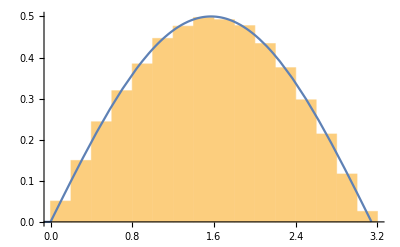

```mathematica
samples =RandomVariate[distθ,100000];

Show[Histogram[samples,Automatic,"PDF"],Plot[PDF[distθ,θ],{θ,-π,π}]]
```

```mathematica
point :=Module[{θ,ϕ, result},
{θ,ϕ} =Sample;
result = {Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ] }
];
points = point &/@Range[100];
listofpoints=points;

ClearAll[sphereMesh]
sphereMesh[n_:40,m_:40,opts:OptionsPattern[]]:=Module[{tr1=AffineTransform[{{{Sin@#,0,0},{0,Sin@#,0},{0,0,1}},{0,0,Cos@#}}]&/@Subdivide[0,2 Pi,n],tr2=RotationTransform[#,{0,0,1}]&/@Subdivide[0,2 Pi,m],cp=Join[#,{First@#}]&[CirclePoints[50]],cxy,cyz},cxy=Line[Append[0]/@cp];
cyz=Line[Insert[0,1]/@cp];
Graphics3D[{Opacity[0.5],Gray,MapThread[GeometricTransformation,{{cxy,cyz},{tr1,tr2}}]},Boxed->False,opts]]
```

```mathematica
newpoint[α_,μ_,pt_]:=Module[{result,θ,ϕ,θnew,soln},
If[Abs[pt[[3]]]==1,
pt,
θ=ArcCos[pt[[3]]];
{soln}=Quiet[NSolve[pt[[1]]/Sin[θ]+ⅈ pt[[2]]/Sin[θ]==ⅇ^(ⅈ ϕ),ϕ]];
θnew = 2 ArcCos[(Cos[θ/2] ℳ[0,0,α]/ℳ[0,0,μ α])/(√((Cos[θ/2] ℳ[0,0,α]/ℳ[0,0,μ α])^2+(Sin[θ/2] ℳ[1,0,α]/ℳ[1,0,μ α])^2))];
ϕ=Simplify[Re[ϕ]/.soln,C[1]==0];
{Sin[θnew]Cos[ϕ],Sin[θnew]Sin[ϕ],Cos[θnew] }
]
];
```

```mathematica
SingleQubitCliffordUnitaries:=Module[{result},
Id=PauliMatrix[0];
H = HadamardMatrix[2];
S = √PauliMatrix[3];
Subscript[ρ, 0]= {{1,0},{0,0}};
result =(# .Subscript[ρ, 0].#†)&/@{Id,H,S,H.S,S.H,S.S,H.S.H,H.S.S,S.H.S,S.S.H,S.S.S,H.S.H.S,H.S.S.H,H.S.S.S,S.H.S.S,S.S.H.S,H.S.H.S.S,H.S.S.H.S,S.H.S.S.H,S.H.S.S.S,S.S.H.S.S,H.S.H.S.S.H,H.S.H.S.S.S,H.S.S.H.S.S}
(* There are 24 Clifford unitaries for a single qubit: *)
];
BlochVector[ρ_]:=N[Re[Tr[ρ.PauliMatrix[#]]]]&/@{1,2,3};
ThreeDesignpoints = BlochVector[#]&/@SingleQubitCliffordUnitaries;
```

```mathematica
MatrixForm[H.S.H.{{1,0},{0,0}}.(H.S.H)†]
```

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

```mathematica
Norm/@ThreeDesignpoints
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Show[{sphereMesh[50,20],ListPointPlot3D[ThreeDesignpoints ,PlotRange->Full,BoxRatios->{1, 1, 1},Axes->False]},ImageSize->Large]
```

-Graphics3D-

5 - design

```mathematica
(* Ref. Quantum 4,325 (2020) and J.Math.Phys.48,052104 2007*)
ClearAll[ω];
e =PauliMatrix[0];
g1 = - PauliMatrix[0];
g2 = {{-ω^11-ω^14,-ω^11-ω^14},{ω^10,-ω-ω^4}};
g3 ={{-ω-ω^2-ω^4-ω^8-2(ω^11+ω^14),ω^6+ω^9},{ω^11+ω^14,-ω^5}};
MatrixForm/@{g1,g2,g3}
ω =ⅇ^(ⅈ 2 π/15);
g2=FullSimplify[g2];
g3=FullSimplify[g3];
```

{(-1 | 0
0 | -1),(-ω^11-ω^14 | -ω^11-ω^14
ω^10 | -ω-ω^4),(-ω-ω^2-ω^4-ω^8-2 (ω^11+ω^14) | ω^6+ω^9
ω^11+ω^14 | -ω^5)}

```mathematica
GroupElementsFromGeneratorsBruteForce[e_,G_]:=
(* Ref: user154997,Generate all elements of a point group from generating set,URL (version:2017-10-04):https://physics.stackexchange.com/q/351400 *)
Module[{L,ΔG, dimL, dimG, new,j,k,g,h,gh},
L = {e};
ΔG = Dimensions[G][[1]];(*new elements added to the result *)

Print[ΔG];
While [ΔG>0,
new={};
Monitor[
dimL= Dimensions[L][[1]];
dimG = Dimensions[G][[1]];
For[j=1,j<=dimL,j++,
For[k=1, k<=dimG,k++,
g=L[[j]];
h=G[[k]];
gh = FullSimplify[g.h];
If[MemberQ[L,gh]==False,
AppendTo[new,gh];
AppendTo[L,gh]];
];
];
ΔG = Dimensions[new][[1]];
,{dimL,ΔG}];
];
L
];
```

```mathematica
GroupElementsFromGeneratorsCosetMethod[e_,G_]:=
(* Ref: user154997,Generate all elements of a point group from generating set,URL (version:2017-10-04):https://physics.stackexchange.com/q/351400 *)
Module[{L,g,g1,dimG,C, L1, new, more,dimC,s,sg,dimL1,t,sgt,j,k,l,m},
Monitor[
here=0;
L = {e};
g=FullSimplify[G[[1]]];
g1=g;
While[g!=e,
AppendTo[L,g];
g =FullSimplify[g.g1];
];
dimG=Dimensions[G][[1]];
For[j=0, j<=dimG, j++,
C = {e};
L1 = L;
more =True;
While[more,
more=False;
dimC=Dimensions[C][[1]];
For[k=1,k<=dimC,k++,
g=C[[k]];
For[l=1,l<=j,l++,
s=G[[l]];
sg =FullSimplify[s.g];
here=l;
If[MemberQ[L,sg]==False,
AppendTo[C,sg];
dimL1 = Dimensions[L1][[1]];
For[m=1,m<=dimL1,m++,
t=L1[[m]];
sgt=FullSimplify[sg.t];
AppendTo[L,sgt];
];
more=True;
];
];
];
];
];
,{Dimensions[L][[1]],here}];
L
];
```

```mathematica
L=GroupElementsFromGeneratorsCosetMethod[e,{g1,g2,g3}]
```

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{(-1)^(7/15) (1+(-1)^(2/5)),(-1)^(7/15) (1+(-1)^(2/5))},{-(-1)^(1/3),-(-1)^(2/15) (1+(-1)^(2/5))}},{{-(-1)^(7/15) (1+(-1)^(2/5)),-(-1)^(7/15) (1+(-1)^(2/5))},{(-1)^(1/3),(-1)^(2/15)+(-1)^(8/15)}},{{Root0.309-2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,3]0.30901699437494745,1/4 (1-ⅈ √3) (3+√5)},{Root0.809+1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,4]0.8090169943749475,Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745}},{{-Root0.309-2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,3]0.30901699437494745,1/4 ⅈ (ⅈ+√3) (3+√5)},{Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475,-Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745}},{{Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745,Root-1.31+2.27 ⅈRoot[1+3 #1+8 #1^2+3 #1^3+#1^4&,2]-1.3090169943749475},{Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475,Root0.309-2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,3]0.30901699437494745}},167,{{Root-2.12+0.866 ⅈRoot[4+2 #1+5 #1^2+4 #1^3+#1^4&,2]-2.118033988749895,Root-2.12-0.866 ⅈRoot[4+2 #1+5 #1^2+4 #1^3+#1^4&,1]-2.118033988749895},{Root1.31-2.27 ⅈRoot[1-3 #1+8 #1^2-3 #1^3+#1^4&,3]1.3090169943749475,1+Root1.12-0.866 ⅈRoot[4-#1^2+#1^4&,3]1.118033988749895}},{{1+Root1.12-0.866 ⅈRoot[4-#1^2+#1^4&,3]1.118033988749895,1+Root1.12+0.866 ⅈRoot[4-#1^2+#1^4&,4]1.118033988749895},{Root-1.31+2.27 ⅈRoot[1+3 #1+8 #1^2+3 #1^3+#1^4&,2]-1.3090169943749475,Root-2.12+0.866 ⅈRoot[4+2 #1+5 #1^2+4 #1^3+#1^4&,2]-2.118033988749895}},{{Root0.809-1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,3]0.8090169943749475,1},{Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745,Root-0.809+1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,2]-0.8090169943749475}},{{Root-0.809+1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,2]-0.8090169943749475,-1},{Root-0.309-2.27 ⅈRoot[4-8 #1+5 #1^2-#1^3+#1^4&,1]-0.30901699437494745,Root0.809-1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,3]0.8090169943749475}},{{Root0.809+1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,4]0.8090169943749475,1/2 (1+ⅈ √3)},{Root-1.81-1.40 ⅈRoot[4+10 #1+11 #1^2+5 #1^3+#1^4&,1]-1.8090169943749475,Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475}},{{Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475,-1/2 ⅈ (-ⅈ+√3)},{1/4 (5+√5+ⅈ √(6 (3+√5))),Root0.809+1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,4]0.8090169943749475}}}
 |  |  |  |

```mathematica
Dimensions[L]
```

{180,2,2}

Incorrect!

```mathematica
FullSimplify[L]
```

{{{1,0},{0,1}},{{-1,0},{0,-1}},{{(-1)^(7/15) (1+(-1)^(2/5)),(-1)^(7/15) (1+(-1)^(2/5))},{-(-1)^(1/3),-(-1)^(2/15) (1+(-1)^(2/5))}},{{-(-1)^(7/15) (1+(-1)^(2/5)),-(-1)^(7/15) (1+(-1)^(2/5))},{(-1)^(1/3),(-1)^(2/15)+(-1)^(8/15)}},{{Root0.309-2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,3]0.30901699437494745,1/4 (1-ⅈ √3) (3+√5)},{Root0.809+1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,4]0.8090169943749475,Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745}},{{-Root0.309-2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,3]0.30901699437494745,1/4 ⅈ (ⅈ+√3) (3+√5)},{Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475,-Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745}},{{Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745,Root-1.31+2.27 ⅈRoot[1+3 #1+8 #1^2+3 #1^3+#1^4&,2]-1.3090169943749475},{Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475,Root0.309-2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,3]0.30901699437494745}},167,{{Root-2.12+0.866 ⅈRoot[4+2 #1+5 #1^2+4 #1^3+#1^4&,2]-2.118033988749895,Root-2.12-0.866 ⅈRoot[4+2 #1+5 #1^2+4 #1^3+#1^4&,1]-2.118033988749895},{Root1.31-2.27 ⅈRoot[1-3 #1+8 #1^2-3 #1^3+#1^4&,3]1.3090169943749475,1+Root1.12-0.866 ⅈRoot[4-#1^2+#1^4&,3]1.118033988749895}},{{1+Root1.12-0.866 ⅈRoot[4-#1^2+#1^4&,3]1.118033988749895,1+Root1.12+0.866 ⅈRoot[4-#1^2+#1^4&,4]1.118033988749895},{Root-1.31+2.27 ⅈRoot[1+3 #1+8 #1^2+3 #1^3+#1^4&,2]-1.3090169943749475,Root-2.12+0.866 ⅈRoot[4+2 #1+5 #1^2+4 #1^3+#1^4&,2]-2.118033988749895}},{{Root0.809-1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,3]0.8090169943749475,1},{Root0.309+2.27 ⅈRoot[4+8 #1+5 #1^2+#1^3+#1^4&,4]0.30901699437494745,Root-0.809+1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,2]-0.8090169943749475}},{{Root-0.809+1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,2]-0.8090169943749475,-1},{Root-0.309-2.27 ⅈRoot[4-8 #1+5 #1^2-#1^3+#1^4&,1]-0.30901699437494745,Root0.809-1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,3]0.8090169943749475}},{{Root0.809+1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,4]0.8090169943749475,1/2 (1+ⅈ √3)},{Root-1.81-1.40 ⅈRoot[4+10 #1+11 #1^2+5 #1^3+#1^4&,1]-1.8090169943749475,Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475}},{{Root-0.809-1.40 ⅈRoot[1-#1+2 #1^2+#1^3+#1^4&,1]-0.8090169943749475,-1/2 ⅈ (-ⅈ+√3)},{1/4 (5+√5+ⅈ √(6 (3+√5))),Root0.809+1.40 ⅈRoot[1+#1+2 #1^2-#1^3+#1^4&,4]0.8090169943749475}}}
 |  |  |  |

```mathematica
Dimensions[L]
```

{4,2,2}

```mathematica
Repetitions[g_]:=
Module[{n,element},
n=1;
element =g;
While[n<=120&&element!=PauliMatrix[0],
n++;
element =FullSimplify[element.g];
];
n
];
```

```mathematica
Simplify[MatrixPower[g2,120]]//MatrixForm
```

```mathematica
L={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2]};
```

```mathematica
AppendTo[L,PauliMatrix[1]]
```

{{{1,0},{0,1}},{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{0,1},{1,0}}}

```mathematica
newpoints[α_,μ_,points_]:=newpoint[α,μ,#]&/@points;
arc[{start_?VectorQ,end_?VectorQ}]:=
Module[{ang,co,r},
center={0,0,0};
ang=VectorAngle[start-center,end-center];
co=Cos[ang/2];
r=EuclideanDistance[center,start];
Arrow[BSplineCurve[{start,center+r/co Normalize[(start+end)/2-center],end},SplineDegree->2,SplineKnots->{0,0,0,1,1,1},SplineWeights->{1,co,1}]]
];
```

```mathematica
ClearAll[listofarrows];
listofarrows[α_,μ_,points_]:=Graphics3D/@{Red,Thickness[0.0028],Arrowheads[.018],arc/@Thread[{points,newpoints[α,μ,points]}]};

plt = Show[{
Graphics3D[{Opacity[0.85],Lighting->{"Ambient",White},White,Sphere[]},Axes->False],sphereMesh[50,20],
listofarrows[1,√0.85,ThreeDesignpoints]
}
,ImageSize->Large,Boxed->False,PlotRange->{{-1,1},{-1,1},{-1,1}},ImagePadding->None,Method->{"ShrinkWrap"->True}]
(*Export["mu2=.50.pdf",plt]*)
```

-Graphics3D-

```mathematica
newlistofpoints= newpoints[1,√0.50,listofpoints];
ClearAll[listofarrows];
listofarrows=Graphics3D/@{Red,Thickness[0.0028],Arrowheads[.018],arc/@Thread[{listofpoints,newlistofpoints}]};
plt = Show[{Graphics3D[{Opacity[0.85],Lighting->{"Ambient",White},White,Sphere[]},Axes->False],sphereMesh[50,20],listofarrows},ImageSize->Large,Boxed->False,PlotRange->{{-1,1},{-1,1},{-1,1}},ImagePadding->None,Method->{"ShrinkWrap"->True}]
(*Export["mu2=.50.pdf",plt]*)
```

-Graphics3D-

```mathematica
newlistofpoints= newpoints[1,√0.80,listofpoints];
listofarrows=Graphics3D/@{Red,Thickness[0.0028],Arrowheads[.018],arc/@Thread[{listofpoints,newlistofpoints}]};
plt = Show[{Graphics3D[{Opacity[0.85],Lighting->{"Ambient",White},White,Sphere[]},Axes->False],sphereMesh[50,20],listofarrows},ImageSize->Large,Boxed->False,PlotRange->{{-1,1},{-1,1},{-1,1}},ImagePadding->None,Method->{"ShrinkWrap"->True}]
(*Export["mu2=.80.pdf",plt]*)
```

-Graphics3D-

```mathematica
newlistofpoints= newpoints[1,√2,listofpoints];
listofarrows=Graphics3D/@{Blue,Thickness[0.0028],Arrowheads[.018],arc/@Thread[{listofpoints,newlistofpoints}]};
plt = Show[{Graphics3D[{Opacity[0.85],Lighting->{"Ambient",White},White,Sphere[]},Axes->False],sphereMesh[50,20],listofarrows},ImageSize->Large,Boxed->False,PlotRange->{{-1,1},{-1,1},{-1,1}},ImagePadding->None,Method->{"ShrinkWrap"->True}]
(*Export["mu2=2.pdf",plt]*)
```

-Graphics3D-

```mathematica
Show[{sphereMesh[50,20],ListPointPlot3D[listofpoints,PlotRange->Full,BoxRatios->{1, 1, 1},Axes->False]},ImageSize->Large]
```

-Graphics3D-

```mathematica
Show[{sphereMesh[50,20],ListPointPlot3D[newpoints[2,√(.1),listofpoints],PlotRange->Full,BoxRatios->{1, 1, 1},Axes->False]},ImageSize->Large]
```

-Graphics3D-